```mathematica
ListaC={{0,6},
{1,1},
{2,1},
{3,1},
{4,2},
{5,1},
{6,10},
{7,11},
{8,17},
{9,24},
{10,23},
{11,39},
{12,62},
{13,61},
{14,82},
{15,107},
{16,108},
{17,157},
{18,172},
{19,194},
{20,240},
{21,242},
{22,354},
{23,362},
{24,394},
{25,458},
{26,470},
{27,575},
{28,584},
{29,646},
{30,671},
{31,664},
{32,693},
{33,814},
{34,753},
{35,782},
{36,861},
{37,853},
{38,927},
{39,896},
{40,876},
{41,926},
{42,862},
{43,849},
{44,821},
{45,898},
{46,768},
{47,744},
{48,742},
{49,767},
{50,659},
{51,676},
{52,623},
{53,605},
{54,600},
{55,560},
{56,544},
{57,514},
{58,495},
{59,438},
{60,471},
{61,402},
{62,435},
{63,399},
{64,378},
{65,369},
{66,345},
{67,318},
{68,296},
{69,275},
{70,265},
{71,256},
{72,208},
{73,197},
{74,172},
{75,133},
{76,128},
{77,103},
{78,89},
{79,83},
{80,37},
{81,23},
{82,28},
{83,15},
{84,13},
{85,7},
{86,3},
{87,4},
{88,1},
{89,1},
{90,1}}
```

{{0,6},{1,1},{2,1},{3,1},{4,2},{5,1},{6,10},{7,11},{8,17},{9,24},{10,23},{11,39},{12,62},{13,61},{14,82},{15,107},{16,108},{17,157},{18,172},{19,194},{20,240},{21,242},{22,354},{23,362},{24,394},{25,458},{26,470},{27,575},{28,584},{29,646},{30,671},{31,664},{32,693},{33,814},{34,753},{35,782},{36,861},{37,853},{38,927},{39,896},{40,876},{41,926},{42,862},{43,849},{44,821},{45,898},{46,768},{47,744},{48,742},{49,767},{50,659},{51,676},{52,623},{53,605},{54,600},{55,560},{56,544},{57,514},{58,495},{59,438},{60,471},{61,402},{62,435},{63,399},{64,378},{65,369},{66,345},{67,318},{68,296},{69,275},{70,265},{71,256},{72,208},{73,197},{74,172},{75,133},{76,128},{77,103},{78,89},{79,83},{80,37},{81,23},{82,28},{83,15},{84,13},{85,7},{86,3},{87,4},{88,1},{89,1},{90,1}}

```mathematica
L=Length[ListaC]
```

91

```mathematica
∑_(j=1)^L ListaC[[j]][[2]]
```

32740

```mathematica
μ=N[∑_(j=1)^L ((ListaC[[j]][[1]]*ListaC[[j]][[2]])/32740)]
```

44.1075

```mathematica
σ=N[√(∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^2*ListaC[[j]][[2]])/32739))]
```

14.6175

```mathematica
σ^2
```

213.672

```mathematica
Subscript[CA, F]=∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^3*ListaC[[j]][[2]])/(32739*σ^3))
```

0.22224

```mathematica
K=∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^4*ListaC[[j]][[2]])/(32739*σ^4))-3
```

-0.459913

```mathematica
Length[ListaC]
```

91

```mathematica
Lista2=Table[{ListaC[[j]][[1]],(ListaC[[j]][[2]])/32740},{j,1,Length[ListaC]}];
```

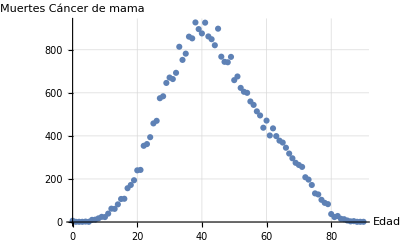

```mathematica
g1=ListPlot[ListaC ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de mama"}]
```

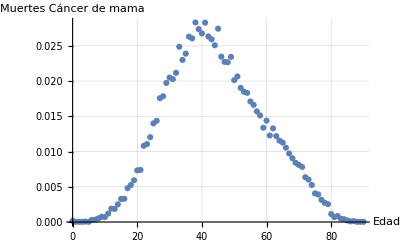

```mathematica
g3=ListPlot[Lista2 ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de mama"}]
```

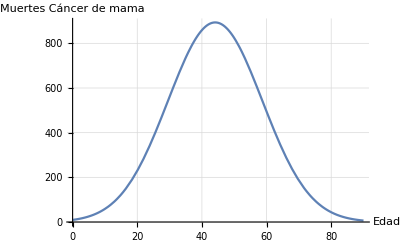

```mathematica
g2=Plot[32740*1/(√(2π)σ) ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,90},GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer de mama"}]
```

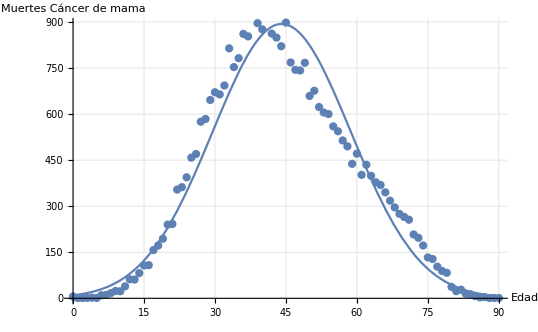

```mathematica
Show[g2,g1]
```